```mathematica
ClearAll["Global`*"]
```

## Import experimental data

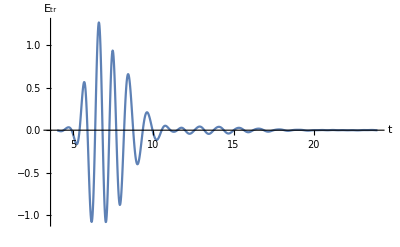

```mathematica
(*data=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\data.csv","Data"]
data[[All,1]]*=10^12;*)
messyData=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\epsdata.txt"];
lessMessyData=ToExpression@StringReplace[StringSplit[messyData],"e"->"*10^"];
data=Table[{lessMessyData[[i]],lessMessyData[[i+1]]},{i,1,Length[lessMessyData]-1,2}];
tmin=data[[1,1]];
tmax=data[[-1,1]];
ListLinePlot[data,PlotRange->All,AxesLabel->{Style["t",Black,14],Style["E_tr",Black,14]}]
```

## Main constants

```mathematica
z=1. 10^-3;(*detector position*)
c=3. 10^8;
n0=1;
τp=.5 10^-12;
f0=1. 10^12;
k0=2 π f0/c;
fmin=0.5 10^12; 
fmax=1.5 10^12;
divisionNumber=100;
d=1. 10^-3;
interpOrder=3;
maxIters=500;
```

## Main formulas

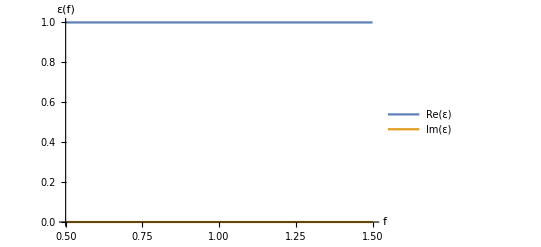

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
timeDomain=Transpose[data][[1]];
discreteExponent[f_]:=Transpose[{timeDomain,Exp[I 2π f(t-z/c)]/.{t->timeDomain}}]
multipliedFuncValues[f_]:=Transpose[data][[2]]*Transpose[discreteExponent[f]][[2]]
RealMultipliedFunction[f_]:=Transpose[{timeDomain,Re@multipliedFuncValues[f]}]
ImMultipliedFunction[f_]:=Transpose[{timeDomain,Im@multipliedFuncValues[f]}]
RealIntegral[f_]:=Integrate[Interpolation[RealMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
ImIntegral[f_]:=Integrate[Interpolation[ImMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
RealT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*RealIntegral[f]
ImT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*ImIntegral[f]
Φ[f_,n_,k0_,d_,τ_,f0_]:=(4n)/((n+1)^2 Exp[-I k0 n d]-(n-1)^2 Exp[I k0 n d])-(RealT[f,τ,f0]+I ImT[f,τ,f0])
fArray=N[Subdivide[fmin,fmax,divisionNumber]];
nFinder[f_,k0_,d_,τp_,f0_,n0_]:=Quiet@FindRoot[Φ[f,n,k0,d,τp,f0],{n,n0},Method->"AffineCovariantNewton"]
fnArray=ParallelTable[{fArray[[i]],nFinder[fArray[[i]],k0,d,τp,f0,n0][[1,2]]},{i,1,Length[fArray]}];
fϵArray=Transpose[{fArray,fnArray[[All,2]]^2}];
fϵRealArray=Transpose[{fArray,Re[fϵArray[[All,2]]]}];
fϵImArray=Transpose[{fArray,Im[fϵArray[[All,2]]]}];
InterpolatedRealϵ=Interpolation[fϵRealArray,InterpolationOrder->interpOrder];
InterpolatedImϵ=Interpolation[fϵImArray,InterpolationOrder->interpOrder];
Plot[{InterpolatedRealϵ[f],InterpolatedImϵ[f]},{f,fmin,fmax},PlotRange->All,PlotLegends->{"Re(ε)","Im(ε)"},AxesLabel->{Style["f",Black,14],Style["ε(f)",Black,14]}]
```

```mathematica
n0=.5;
```

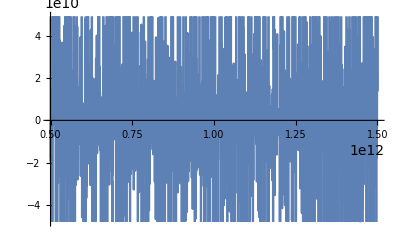

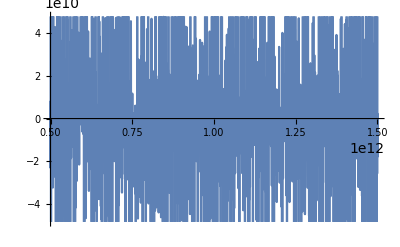

```mathematica
Plot[RealT[f,τp,f0],{f,fmin,fmax}]
Plot[ImT[f,τp,f0],{f,fmin,fmax}]
```

## Fun

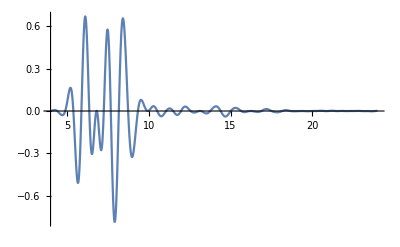

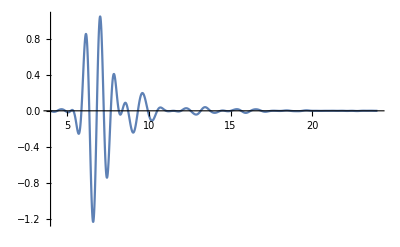

```mathematica
intfunc1=Interpolation[RealMultipliedFunction[1],InterpolationOrder->3];
intfunc2=Interpolation[ImMultipliedFunction[1],InterpolationOrder->3];
Plot[intfunc1[t],{t,tmin,tmax},PlotRange->All]
Plot[intfunc2[t],{t,tmin,tmax},PlotRange->All]
```

```mathematica
fϵArray
```

{{5.×10^11,1.},{5.1×10^11,1.},{5.2×10^11,1.},{5.3×10^11,1.},{5.4×10^11,1.},{5.5×10^11,1.},{5.6×10^11,1.},{5.7×10^11,1.},{5.8×10^11,1.},{5.9×10^11,1.},{6.×10^11,1.},{6.1×10^11,1.},{6.2×10^11,1.},{6.3×10^11,1.},{6.4×10^11,1.},{6.5×10^11,1.},{6.6×10^11,1.},{6.7×10^11,1.},{6.8×10^11,1.},{6.9×10^11,1.},{7.×10^11,1.},{7.1×10^11,1.},{7.2×10^11,1.},{7.3×10^11,1.},{7.4×10^11,1.},{7.5×10^11,1.},{7.6×10^11,1.},{7.7×10^11,1.},{7.8×10^11,1.},{7.9×10^11,1.},{8.×10^11,1.},{8.1×10^11,1.},{8.2×10^11,1.},{8.3×10^11,1.},{8.4×10^11,1.},{8.5×10^11,1.},{8.6×10^11,1.},{8.7×10^11,1.},{8.8×10^11,1.},{8.9×10^11,1.},{9.×10^11,1.},{9.1×10^11,1.},{9.2×10^11,1.},{9.3×10^11,1.},{9.4×10^11,1.},{9.5×10^11,1.},{9.6×10^11,1.},{9.7×10^11,1.},{9.8×10^11,1.},{9.9×10^11,1.},{1.×10^12,1.},{1.01×10^12,1.},{1.02×10^12,1.},{1.03×10^12,1.},{1.04×10^12,1.},{1.05×10^12,1.},{1.06×10^12,1.},{1.07×10^12,1.},{1.08×10^12,1.},{1.09×10^12,1.},{1.1×10^12,1.},{1.11×10^12,1.},{1.12×10^12,1.},{1.13×10^12,1.},{1.14×10^12,1.},{1.15×10^12,1.},{1.16×10^12,1.},{1.17×10^12,1.},{1.18×10^12,1.},{1.19×10^12,1.},{1.2×10^12,1.},{1.21×10^12,1.},{1.22×10^12,1.},{1.23×10^12,1.},{1.24×10^12,1.},{1.25×10^12,1.},{1.26×10^12,1.},{1.27×10^12,1.},{1.28×10^12,1.},{1.29×10^12,1.},{1.3×10^12,1.},{1.31×10^12,1.},{1.32×10^12,1.},{1.33×10^12,1.},{1.34×10^12,1.},{1.35×10^12,1.},{1.36×10^12,1.},{1.37×10^12,1.},{1.38×10^12,1.},{1.39×10^12,1.},{1.4×10^12,1.},{1.41×10^12,1.},{1.42×10^12,1.},{1.43×10^12,1.},{1.44×10^12,1.},{1.45×10^12,1.},{1.46×10^12,1.},{1.47×10^12,1.},{1.48×10^12,1.},{1.49×10^12,1.},{1.5×10^12,1.}}